# Lab 4 – Compartmental and spatial models

Week 4: We will look at compartmental and spatial modeling in (mainly cellular) biology and some of the differences between these two approaches.

## Background

In biology many processes are either happening in different compartments and/or are spatially separated. For instance, gene transcription in eukaryotes is taking place in the cell nucleus (Fig. 1.). The transcripts (mRNAs) encoding a protein for instance, are then transported to the (rough) endoplasmic reticulum studded with ribosomes. These ribosomes can translate the mRNA strands into proteins. Proteins can be packaged into vesicles and transported to the Golgi apparatus, where they fuse with the Golgi membranes and are modified. Thereafter they are transported further to the their final destination outside or inside the cell. Outside the cells, they can be transported to different tissues etc. 

-Graphics-
Figure 1: Eukarytoic cell organelles. 1. Cell nucleus, 2. nuclear pore, 3. rough endoplasmic reticulum, 4. smooth endoplasmic reticulum, 5. ribosome, 6. protein being transported, 7. transport vesicle, 8. Golgi apparatus, 9. Cis face of the Golgi apparatus, 10. Trans face of the Golgi apparatus, 11. Cisternae of the Golgi apparatus.

If molecules diffuse freely and independently and if diffusion is much faster than chemical reactions, inhomogeneities will disappear and substances may be described by concentrations averaged over a cell (Klipp et al., 2009). If molecules are not homogeneously distributed because of membranes for instance, then spatial location and structures need to be modeled. The spatiotemporal dynamics of substances and their concentrations can be modeled by different mathematical frameworks, which include compartmental models (e.g. modelling organelles), reaction-diffusion equations and stochastic simulations.
 
Spatial processes are also found in for instance populations of bacteria or animals. Each individual or a group can migrate and travel (long or short) distances. Think for instance of the famous and largest terrestrial mammal migration in the Serengeti (which can influence the way predators attack or change feeding patterns etc.).

Compartmental modeling

A multi-compartmental model is a mathematical model used for describing how materials/energies are transported between different compartments of a system (e.g. cellular organelles). The compartments are assumed to each be homogeneous. It is assumed there is fast diffusion in the compartments, and if the compartments resemble each other and rapid mixing between them would not make a difference, they can be treated as a single compartment. 

To make multi-compartmental modeling easier, certain assumptions can be made (that rarely exist in reality), by assuming a certain “topology”, with the most known: 

- Closed model (sinks and sources do not exist)
- Open model (sinks and sources do exist) 

In principle, you can think of a multi-compartmental model as a set of blocks, each representing a compartment, connected to each other in some way (Figure 2). Let us look at a simple example. 

-Graphics-
Figure 2: Schematic representation of compartmental model. 

Let’s assume we are looking at a compartmental model with an exchange of substances, e.g. ions/enzymes. We can in general denote the concentration in compartment i, as C_i with (1 ≤ i ≤ n). In the diagram above n = 2. The rate of change would be: 

	(ⅆ C_i)/ⅆt=α_i ( ∑J_in-∑ J_out)    

with α_ia parameter related to the volume of the compartment i, ∑J_in the sum of fluxes into the compartments and ∑ J_out the sum of fluxes out of the compartment. The model for the diagram given above would then be: 

	(ⅆ C_1)/ⅆt=α_1 ( J_21- J_12)
(ⅆ C_2)/ⅆt=α_2 ( J_12- J_21)

Reaction-diffusion systems

The shapes and sizes of cells and/or compartments and spatial distribution of molecules inside of them can control how molecules interact to produce a certain cellular behaviour.
Diffusion describes the space- and time-dependent concentration change of a substance. The reaction-diffusion system describes several substances that diffuse and participate in reactions. Combining a kinetic model for chemical reactions and the diffusion equation a reaction-diffusion equation is obtained. Most of these models can only be solved numerically, i.e. with finite element methods, because of nonlinearity.  
The general reaction-diffusion equations is given by:

	(∂u)/(∂t)=D_u∇^2 u+f(u)

with D_uthe diffusion constant of u and f(u) the function describing the reaction kinetics (formation and decay) of u.   
Reaction-diffusion systems can show various kinds of dynamic behaviour.  A famous example is pattern formation (Figure 3). Alan Turing proposed the theory (in 1952) that the patterns we see in nature, such as pigmentation in animals, branching trees and skeletal structures are reflections of inhomogeneities in the underlying biochemical signalling (Maini, P.K., et al. 2012). 

-Graphics-
Figure 3: Pattern formation. Animal markings (top two pictures). Lower left, Drosophila melanogaster gene expression of different genes in patterns during embryogenesis. Lower right, single bacteria colony growing in chiral patterns in search for food.   

Patterns can form spontaneously from systems that have a homogeneous steady state. The steady state must be stable against homogeneous concentration changes, but unstable against spatial variation (diffusion). In essence, diffusion is usually the stabilizing and homogenizing process, but Turing showed that from the interaction of two stabilizing processes, an instability could emerge. 
The conditions described above can be fulfilled in a simple reaction-diffusion system with two substances called the activator (u) and inhibitor (v) (aka morphogens) as shown in Figure 4. If the inhibitor diffuses faster than the activator, the activator piles up in local regions in space, forming steady state patterns (dots or stripes). In other words, the inhibitor diffuses faster, inhibiting the production of the activator A over a long range (negative  feedback dominated the long distance). Activator A will only spread locally, thus forming locally high concentrations (positive feedback dominates the short distance).
-Graphics-
Figure 4: Activator and inhibitor graph.

The forms of the reaction kinetics (f(u)) depend on the problem at hand. For the above (Figure 4) example, the reaction terms are given by the following: 

	f(u,v)=-u +u^p/v^q
g(u,v)=-v +u^r/v^s

where  1<(q r)/((p - 1)(s + 1)),1<p 

(after scaling). 

This system is commonly called the Grierer-Meinhardt system. 
The effect of the activator and inhibitor can be clearly seen from the reaction terms. The activator appears in the numerator of both terms, thus increasing the production of both itself and inhibitor. The inhibitor appears in both the denominators, decreasing the production of the activator. Both equations also have decay due to the negative linear terms.     
Next to initial conditions, boundary conditions are needed so that a unique solution can be guaranteed. Often the Neumann boundary and initial conditions are used, give by: 

	u_x(0,t)=u_x(1,t)= v_x(0,t)= v_x(1,t)= 0
u(x,0)=u_0(x)
v(x,0)=v_0(x)  

for a one-dimensional homogeneous system. 

An interesting special case in the Grierer-Meinhardt system is the parameter choice (p, q, r, s) = (2, 1, 2, 0). We will solve this one-dimensional system as an example, with the initial conditions for u and v: 1 and 2 respectively; the diffusion constants: D_u= 0.02 and D_v= 0.04; over a time period of 500 time units.

{u^(1,0)[t,x]==-u[t,x]+u[t,x]^2/v[t,x]+0.0004 u^(0,2)[t,x],v^(1,0)[t,x]==u[t,x]^2-v[t,x]+0.04 v^(0,2)[t,x],u^(0,1)[t,0]==0,u^(0,1)[t,5]==0,v^(0,1)[t,0]==0,v^(0,1)[t,5]==0,u[0,x]==1,v[0,x]==2}

-Graphics3D-

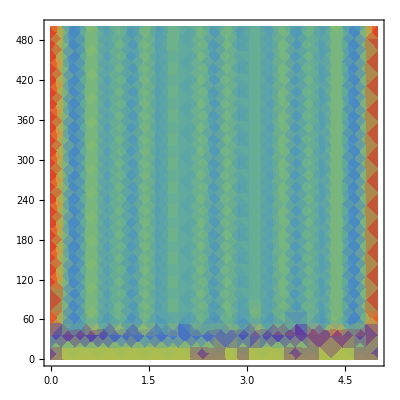

```mathematica
(*define the parameters*)
p= 2;
q = 1;
r = 2;
s = 0;
ϵ = 0.0004;
d = 0.04;
x0=0;
x1=5;
t0=0;
t1=500;
u0=1;
v0=2;
(*define the equations and Neuman boundary conditions (closed)*)
eqs = {D[u[t,x],t] == -u[t,x] + u[t,x]^p/v[t,x]^q+ϵ D[u[t,x],x,x], D[v[t,x],t]==-v[t,x]+u[t,x]^r/v[t,x]^s+d D[v[t,x],x,x],
Derivative[0,1][u][t,x0]==0,
Derivative[0,1][u][t,x1]==0,
Derivative[0,1][v][t,x0]==0,
Derivative[0,1][v][t,x1]==0,
u[t0,x]==u0,
v[t0,x]==v0}

(*solve the system*)
sol=NDSolve[eqs,{u, v}, {t, t0,t1 }, {x, x0,x1 },PrecisionGoal->1];

(*couple of different ways to plot*)
Plot3D[u[t,x]/.sol,{x, x0,x1},{t,t0,t1},ColorFunction->"Rainbow",PlotRange->All,PerformanceGoal->"Quality"]

DensityPlot[v[t,x]/.sol,{x, x0,x1},{t,t0,t1},ColorFunction->"Rainbow",PlotRange->All,PerformanceGoal->"Quality"]

(*plot for u and v vs. time*)
Animate[Plot[{Evaluate[u[t,x]/.sol],Evaluate[v[t,x]/.sol]}, {x,x0,x1}, PlotRange->{0, 10},PlotLegends->{"u - activator", "v - inhibitor"}, PlotStyle->{Orange, Green}],{t,t0,t1,1},AnimationRunning->False]
```

## Exercises

Complex calcium oscillations - A multi-compartmental model

We will start this week with building a multi-compartmental model of intracellular calcium oscillations. Oscillatory changes of cytosolic calcium concentrations (Ca) in response to agonist stimulation are experimentally well observed in various living systems (Marhl et al., 2000) (see paper on Canvas). In the following model we will look at complex behaviour of calcium oscillations, including bursting and chaos. Figure 1 schematically shows the cellular model system, including the Endoplasmic Reticulum (ER), mitochondria and calcium binding proteins in the cytosol, which all can be seen as calcium stores.   

-Graphics-
Figure 3: Schematic representation of the model system. Includes the Endoplasmic Reticulum (ER), mitochondria and calcium binding proteins (Pr) in the cytosol.

Model Description Summary
The number of model variables reduces to three independent variables when applying the conservation relations for total cellular calcium Ca_tot. 

-Graphics-

For the total concentration of bound and unbound proteins Pr_tot the following equation applies:

-Graphics-


The following equations describe the rates of change of calcium in the model:

-Graphics-

-Graphics-

-Graphics-

The fluxes of this model are given by:
-Graphics--Graphics-
-Graphics--Graphics--Graphics-

The model parameters are shown in Table 1: 

-Graphics-

A. First identify the compartments and shortly explain all the terms given in this model. 

There are three compartments in this model: The Endoplasmatic Reticulum, the Mitochondria and the Cytosol. There are two parameters for the total concentrations of Calcium and Calcium binding proteins (Ca), and they are the same the entire simulation, because the model of the cell is closed.

B. Now build this model in Mathematica and use the parameters given in Table 1 with the starting concentrations of cytosolic Ca, ER Ca and mitochondria Ca: 0.3, 0.2 and 1 respectively.

```mathematica
ClearAll["Global`*"]
ClearAll["Global*`"]

(* Define the parameters*)

params={Catot->90,Prtot->120,RhoEr->0.1,RhoM->0.1,BetaEr->0.0025,BetaM->0.0025,Kch->4100,Kpump->20,Kleak->0.05,Kin->300,Kout->125,Km->0.00625,Kplus->0.1,Kmin->0.01,K1->5,K2->0.8,K3->5};

fluxes = {Jpump[t]->  Kpump*Cacyt[t],
     Jch[t]->  Kch*((Cacyt[t]^2)/(K1^2 +Cacyt[t]^2))*(CaEr[t]-Cacyt[t]),
     Jleak[t] ->  Kleak (CaEr[t] - Cacyt[t]),
Jin[t]->  Kin*(Cacyt[t]^8)/(K2^8+Cacyt[t]^8),
Jout[t]->  (Kout * Cacyt[t]^2/(K3^2+Cacyt[t]^2) + Km)* CaMyto[t]};

eqs = {Cacyt'[t] == Jch[t] + Jleak[t] - Jpump[t] + Jout[t] - Jin[t] +Kmin*CaPr[t]-Kplus*Cacyt[t]*Pr[t],
CaEr'[t] == BetaEr *(Jpump[t] - Jch[t] - Jleak[t])/RhoEr,
CaMyto'[t]== BetaM*(Jin[t] -Jout[t])/RhoM,
CaPr[t]== Catot - Cacyt[t] - RhoEr * CaEr[t] / BetaEr - RhoM * CaMyto[t]/BetaM,
Pr[t] == Prtot - CaPr[t],
Cacyt[0] == 0.3, 
CaEr[0] == 0.2, 
CaMyto[0] == 1};

sol = NDSolve[eqs /. fluxes /. params,
{Cacyt[t], CaEr[t], CaMyto[t]}, 
{t, 0, 300}]
```

{{Cacyt[t]→InterpolatingFunction[…][t],CaEr[t]→InterpolatingFunction[…][t],CaMyto[t]→InterpolatingFunction[…][t]}}

B.1. Plot the calcium concentrations of the different compartments over time  and the cytosolic vs. mitochondrial calcium concentrations (from t = 100 to t = 300).  Describe the behaviour you are seeing in both graphs (what can these plots tell you?).

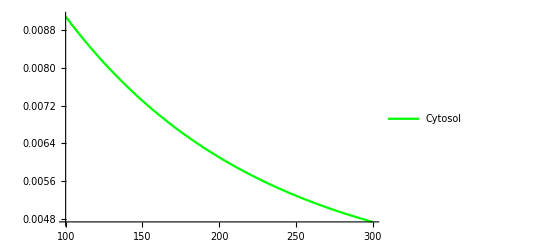

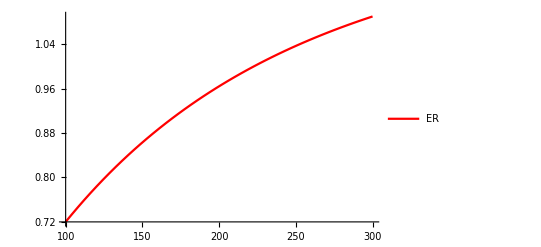

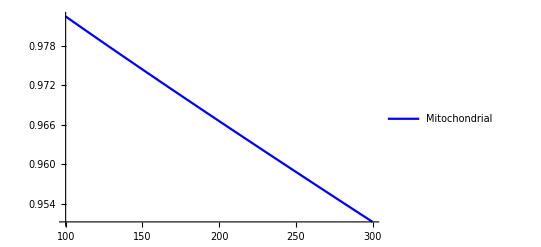

OptionValue::nodef: Unknown option PlotLegends for Graphics.

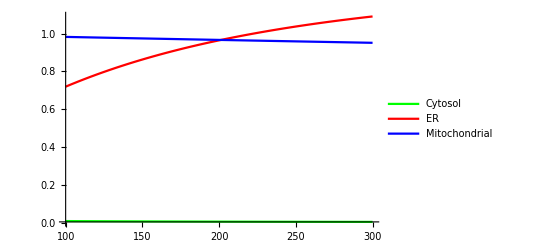

```mathematica
pltCacy = Plot[Cacyt[t] /. sol,{t,100,300}, PlotStyle->Green, PlotLegends->{"Cytosol"}]
pltCaEr = Plot[CaEr[t] /. sol,{t,100,300}, PlotStyle->Red, PlotLegends->{"ER"}]
pltCaMyto = Plot[CaMyto[t] /. sol,{t,100,300}, PlotStyle->Blue, PlotLegends->{"Mitochondrial"}]
(*Deze show is niet echt useful because you don't see Cacyt at all
Misschien log as? idk hoe dat werkt though*)
Show[{pltCacy, pltCaEr, pltCaMyto}, PlotRange->All, PlotLegends -> {"Cytosol","ER", "Mitochondrial" }]
```

C. Change the maximal permeability of the Ca channels to 4000 s^-1 and then 2950 s^-1 (now from t = 0 to t = 300. Explain the behaviour now, when changing this parameter to these two values.

D. Let us assume that due to a genetic mutation, the Ca channel proteins are not transcribed and translated into a functional protein. How would you rewrite the equations of the model? What will happen to the system?

Introduction to pattern formation

A. Give the complete set of reaction-diffusion equations and boundary conditions of the Grierer-Meinhardt system in two-dimensional space.

B. Solve this model with the same parameters as the example in the introduction text and plot u and v patterns.

```mathematica
(*define the parameters*)
p= 2;
q = 1;
r = 2;
s = 0;
ϵ = 0.0004;
d = 0.04;
x0=0;
x1=5;
t0=0;
t1=500;
u0=1;
v0=2;
(*define the equations and Neuman boundary conditions (closed)*)
eqs = {D[u[t,x],t] == -u[t,x] + u[t,x]^p/v[t,x]^q+ϵ D[u[t,x],x,x], D[v[t,x],t]==-v[t,x]+u[t,x]^r/v[t,x]^s+d D[v[t,x],x,x],
Derivative[0,1][u][t,x0]==0,
Derivative[0,1][u][t,x1]==0,
Derivative[0,1][v][t,x0]==0,
Derivative[0,1][v][t,x1]==0,
u[t0,x]==u0,
v[t0,x]==v0}

(*solve the system*)
sol=NDSolve[eqs,{u, v}, {t, t0,t1 }, {x, x0,x1 },PrecisionGoal->1];

(*couple of different ways to plot*)
Plot3D[u[t,x]/.sol,{x, x0,x1},{t,t0,t1},ColorFunction->"Rainbow",PlotRange->All,PerformanceGoal->"Quality"]

DensityPlot[v[t,x]/.sol,{x, x0,x1},{t,t0,t1},ColorFunction->"Rainbow",PlotRange->All,PerformanceGoal->"Quality"]

(*plot for u and v vs. time*)
Animate[Plot[{Evaluate[u[t,x]/.sol],Evaluate[v[t,x]/.sol]}, {x,x0,x1}, PlotRange->{0, 10},PlotLegends->{"u - activator", "v - inhibitor"}, PlotStyle->{Orange, Green}],{t,t0,t1,1},AnimationRunning->False]
```

C. Swap the Grierer-Meinhardt kinetics with another type of the kinetics, the Schnakenberg model. This model is an example of an activator-substrate systems. Here a fast diffusing substrate v is consumed by a slow diffusing activator u.
The kinetics are given by: 

 	f(u,v)=c_1-c_-1 u + c_3 u^2 v
g(u,v) =c_2-c_3 u^2 v 

Solve this model in 2-D, with periodic boundary conditions (x_0 = x_n), on a 100 x 100 space for 1000 time units. The parameters are: D_u=1, D_v=40, u_0=1, v_0=3, c_1=0.1, c_2=0.9, c_-1=1, c_3=1. Describe the patterns you see.

```mathematica
ClearAll["Global`*"]
Du = 1;
Dv = 40;
u0 = 1;
v0 = 3;
c1 = 0.1; 
c2 = 0.9;
c1m = 1;
c3 = 1;

eqs = {f[u_,v_] ==  c1 - c1m u + c3 u^2 v,
g[u_,v_]== c2 - c3 u^2 v}

sol=NDSolve[eqs,{u, v}, {t, 0,1000 }, {x, 0,100 },PrecisionGoal->1];
```

{f[u_,v_]==0.1-u+u^2 v,g[u_,v_]==0.9-u^2 v}

NDSolve::dvnoarg: The function u appears with no arguments.

## References

- Various sources from Wikipedia
- Klipp, E., et al. In book: Systems Biology, A textbook. Chapter 3.  Wiley-Blackwell, 2009. 
- Maini, P.K. et al. (2012). Turing’s model for biological pattern formation and the robustness problem. Interface Focus, 2: 487-496. 
- Marhl, M., et al. (2000). Complex calcium oscillations and the role of mitochondria
and cytosolic proteins. Biosystems, 57: 75-86. 
- Wei, J. & Winter, M. Mathematical aspects of pattern formation in biological systems. Springer. Applied Mathematical Sciences, volume 189.